# Analysis of Sports Scores

## Robert Gotwals

```mathematica
DateString[]
Clear["Global`*"]
```

Thu 1 Dec 2016 13:27:19

## Description of the Data

### Data Import

To import the data, I use the Import command.  Since this data is on the web, I can put a full web address (URL) in quotes with the Import command.  The data is stored as a CSV (comma-separated values) file, built using Microsoft Excel.  This data is stored on the Web at:  http://chemistry.ncssm.edu/medchem/data, and the name of the file is "scores.csv".

```mathematica
data=Import["http://chemistry.ncssm.edu/medchem/data/scores.csv"]
```

{{Name,Pushups,Situps,BallThrow},{Tom,35,65,12},{Ted,74,54,35},{Bob,55,48,29},{Sam,39,84,44},{Luke,45,66,51},{Ed,49,74,22},{Matt,61,68,39}}

### Data Display

I would like to display the data in a little nicer format so I can see how the data is assembled.  You should notice that I have 8 rows of data, and each row has four columns.

```mathematica
data // TableForm
Grid[data, Frame -> All]
```

Name | Pushups | Situps | BallThrow
Tom | 35 | 65 | 12
Ted | 74 | 54 | 35
Bob | 55 | 48 | 29
Sam | 39 | 84 | 44
Luke | 45 | 66 | 51
Ed | 49 | 74 | 22
Matt | 61 | 68 | 39

Name | Pushups | Situps | BallThrow
Tom | 35 | 65 | 12
Ted | 74 | 54 | 35
Bob | 55 | 48 | 29
Sam | 39 | 84 | 44
Luke | 45 | 66 | 51
Ed | 49 | 74 | 22
Matt | 61 | 68 | 39

### Data Length and Referencing

The length of the dataset can be determined with the Length command:

```mathematica
Length[data]
```

8

The data is stored as a list, and can be accessed using data[[row, column]].  For example, the name "Ted" is located at data[[3,1]], and I can point to the name Ted by using data[[3,1]].  Notice the double open and close square brackets!

```mathematica
data[[3,1]]
```

Ted

If I want to see a range of rows or columns, I can use the ;; notation.  For example, if I want to see the last three names (Luke, Ed, and Matt), I can do so as shown below.  Notice that by using "1" in the column location, I only get the information in column 1 (the names).

```mathematica
data[[6;;8,1]]
```

{Luke,Ed,Matt}

### Data Separation

It will be helpful to separate out all of the data from the table into specific variables.  I don’t want the labels in the first row, so I delete them and store them in a new dataset called “datanolabels”,  then I make up the variable names that I want and use the Transpose command to extract data into each of those names:

```mathematica
datanolabels = Delete[data,1];
{name, pushups,situps,ballthrow} = Transpose[datanolabels ]
```

{{Tom,Ted,Bob,Sam,Luke,Ed,Matt},{35,74,55,39,45,49,61},{65,54,48,84,66,74,68},{12,35,29,44,51,22,39}}

```mathematica
situps
```

{65,54,48,84,66,74,68}

I’d like to change the various values from integers to decimal versions of the numbers.  I remNotice that I have an N[] in front of the data boxes.  This converts integer numbers to decimal numbers, making calculations easier later on.

```mathematica
pushups = N[pushups]
situps = N[situps]
ballthrow=N[ballthrow]
```

{35.,74.,55.,39.,45.,49.,61.}

{65.,54.,48.,84.,66.,74.,68.}

{12.,35.,29.,44.,51.,22.,39.}

## Data Analysis and Statistics

### Data Plotting

If I want to plot a variable, such as Pushups (x-axis), I can use the ListPlot or the ListLinePlot command.

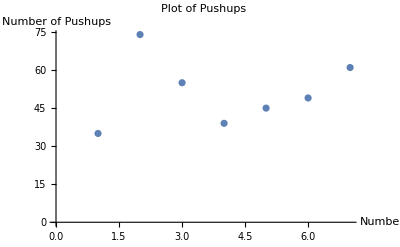

```mathematica
ListPlot[pushups, PlotLabel->"Plot of Pushups", AxesLabel->{"Number", "Number of Pushups"}]
```

If I want to plot two of the variables against each other (say, pushups as x and situps as y), I can do that as below.  The plot is sort of meaningless, since there isn't any relationship between pushups and situps, so the data looks pretty random (because it is!).  Notice that I used PlotRange to plot pushups from 30 to 80 and situps from 10 to 100.

{{35.,65.},{74.,54.},{55.,48.},{39.,84.},{45.,66.},{49.,74.},{61.,68.}}

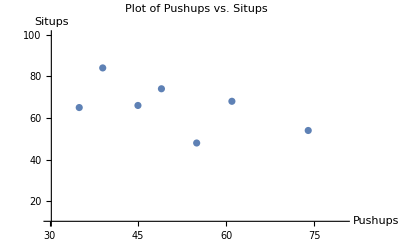

```mathematica
pushsit=Transpose[{pushups,situps}]
ListPlot[pushsit, PlotRange -> {{30,80},{10,100}},PlotLabel->"Plot of Pushups vs. Situps", AxesLabel->{"Pushups","Situps"}]
```

### Descriptive Statistics

Descriptive statistics refers to some of the more fundamental statistical evaluations of data, including Mean (average), Median (the number that separates the upper half from the lower half of the data), the Standard Deviation (a number that shows the distribution of the data), a quartiles listing (three numbers that divides the data into 4 groups), and a graphical display known as a box whisker plot.

To use some of the specialized statistical plots, you need to include a special library known as StatisticalPlots.  Notice the reverse single quote at the end!

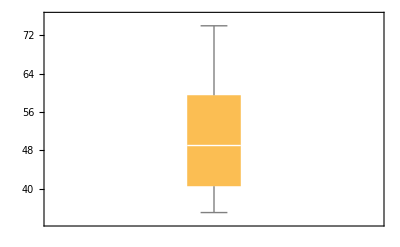
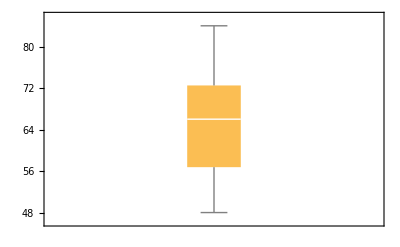
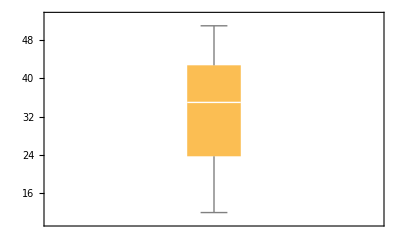
| Pushups | Situps | Throw
Mean | 51.1 | 65.5714 | 33.1429
Median | 49. | 66. | 35.
Standard Deviation | 13.447 | 11.9702 | 13.3095
Quartiles | {40.5,49.,59.5} | {56.75,66.,72.5} | {23.75,35.,42.75}
BoxPlot | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{" ", "Pushups", "Situps", "Throw"}, {"Mean", NumberForm[Mean[pushups],3], Mean[situps], Mean[ballthrow]}, {"Median", Median[pushups], Median[situps], Median[ballthrow]}, {"Standard Deviation", NumberForm[StandardDeviation[pushups],5], StandardDeviation[situps], StandardDeviation[ballthrow]}, {"Quartiles", Quartiles[pushups], Quartiles[situps], Quartiles[ballthrow]}, {"BoxPlot", BoxWhiskerChart[pushups], BoxWhiskerChart[situps], BoxWhiskerChart[ballthrow]}},Frame->All]
```

### Performing a linear regression (line of best fit)

```mathematica
myfit = LinearModelFit[pushsit, x,x];  (* I am doing a regression that I've called "myfit" on the dataset pushsit *)
Normal[myfit]  (* I make it look pretty *)
myfit["RSquared"]  (*I find the correlation coefficient, R-squared, a measure of how good the data fit is *)
```

91.1967-0.501053 x

0.316801

### Data Calculations

Now I want to do some calculations with my dataset.  I am going to create a mathematical equation -- a function -- called "overall".  This function, which depends on variables P_,S_, and T_, creates an overall score, where pushups get 45% of the score, situps 40%,, and the ball throw 15%.  I set this function up as below:

```mathematica
overall[p_,s_,t_] := 0.45 p+ 0.4 s + 0.15 t
```

Now I can calculate an overall score for a given set of scores.  35 pushups, 65 situps, and 12 for the ball throw gives me an overall score of 43.55:

```mathematica
overall[35,65,12]
```

43.55

```mathematica
Print["The overall score is ", overall[35, 65, 12]]
```

The overall score is 43.55

Now I can apply my function to the entire dataset, to get an overall score for everyone in the dataset.  I can use the Transpose command to combine two or more lists.  In this case, I am joining "names" with my newly computed grade for each of the participants.  I call this new (and final) dataset "overall".

```mathematica
name
```

{Tom,Ted,Bob,Sam,Luke,Ed,Matt}

```mathematica
grades=overall[pushups,situps,ballthrow];
results=Transpose[{name,pushups, situps, ballthrow, grades}];
Grid[Prepend[results, {"Name", "Pushups", "Situps", "Ball throw", "Overall score"}],Frame -> All]
```

Name | Pushups | Situps | Ball throw | Overall score
Tom | 35. | 65. | 12. | 43.55
Ted | 74. | 54. | 35. | 60.15
Bob | 55. | 48. | 29. | 48.3
Sam | 39. | 84. | 44. | 57.75
Luke | 45. | 66. | 51. | 54.3
Ed | 49. | 74. | 22. | 54.95
Matt | 61. | 68. | 39. | 60.5

```mathematica
results2 = Table[
{
data[[row, 1]],
data[[row, 2]],
data[[row, 3]],
data[[row, 4]],
overall[data[[row, 2]], data[[row, 3]], data[[row, 4]]]
},
{row, 2, Length[data]}
];
Grid[Prepend[results2, {"Name", "Pushups", "Situps", "Ball throw", "Overall score"}],Frame -> All]
```

Name | Pushups | Situps | Ball throw | Overall score
Tom | 35 | 65 | 12 | 43.55
Ted | 74 | 54 | 35 | 60.15
Bob | 55 | 48 | 29 | 48.3
Sam | 39 | 84 | 44 | 57.75
Luke | 45 | 66 | 51 | 54.3
Ed | 49 | 74 | 22 | 54.95
Matt | 61 | 68 | 39 | 60.5

## Data Filtering

### Data Selection

The code below looks complicated, but if one takes the time to dissect it, it is not too bad.  I want to filter the dataset to reject anyone who can't do at least 50 situps.  That data is placed into a new dataset entitled "rejected", but the rejected person is still in the original database.

```mathematica
Grid[data, Frame -> All]
```

Name | Pushups | Situps | BallThrow
Tom | 35 | 65 | 12
Ted | 74 | 54 | 35
Bob | 55 | 48 | 29
Sam | 39 | 84 | 44
Luke | 45 | 66 | 51
Ed | 49 | 74 | 22
Matt | 61 | 68 | 39

```mathematica
rejected={data[[1,All]]}; (*this gives me the header line*)
Do[
If[
data[[row,3]]< 50,
rejected=Append[rejected,data[[row]]]
],
{row,2,Length[data]}
]
rejected //TableForm
```

Name | Pushups | Situps | BallThrow
Bob | 55 | 48 | 29

Now I want to create a new subset of the original data entitled "accepted".  These are the people who can do 50 or more situps, my criteria for being physically fit.

```mathematica
accepted={data[[1,All]]}; (*this gives me the header line*)
Do[
If[
data[[row,3]]< 50,
accepted=Delete[data,row]
],
{row,2,Length[data]}
]
accepted //TableForm
```

Name | Pushups | Situps | BallThrow
Tom | 35 | 65 | 12
Ted | 74 | 54 | 35
Sam | 39 | 84 | 44
Luke | 45 | 66 | 51
Ed | 49 | 74 | 22
Matt | 61 | 68 | 39

Here is a more complicated but elegant way to do the filtering.  I use the Map/DeleteCases combination, along with the slot (#) notation and the ampersand (&).  The slot is a placeholder, and in this case refers to the dataset “data”.  In this case, I’m only displaying the name (Column 1, or #[[1]]) and the situps (#[[3]]).

```mathematica
Grid[
Map[
{
#[[1]],
#[[2]],
#[[3]],
#[[4]]
} &,
DeleteCases[data, a_ /; a[[3]] < 50]
],
Frame -> All]
```

Name | Pushups | Situps | BallThrow
Tom | 35 | 65 | 12
Ted | 74 | 54 | 35
Sam | 39 | 84 | 44
Luke | 45 | 66 | 51
Ed | 49 | 74 | 22
Matt | 61 | 68 | 39